```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
```

```mathematica
$K=9;
Do[data[k] = {}, {k, 2, 1+$K($K+1)}];
alpha = {};
alphasd  = {};
Do[Module[{}, (
d = Import["../../../backup/mar-14/Stats-101/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"];
Do[AppendTo[data[k], {$N, Around[d[[All, k]]]}], {k, 2, 3}];
AppendTo[alpha, {$N, Around[$K(($N)^2-1)/($N*#)&/@d[[All, 2]]]}];
AppendTo[alphasd, {$N, Around[(√(2$K(($N)^2-1)))/($N*#)&/@d[[All, 3]]]}];
Do[AppendTo[data[k], {$N, Around[d[[All, k]]]}], {k, 4, 1+$K($K+1), 1}];
)], {$N, 3, 9}]
```

```mathematica
fig[1] = ListPlot[alpha,
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"N", "\\alpha_N"},
FrameTicks->{{With[{ticks=15.+4Range[0,10]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->14cm
];
```

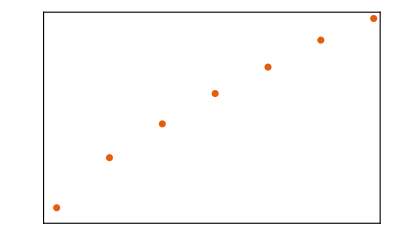

```mathematica
Magnify[fig[1], 1]
```

```mathematica
Export[plotsDir<>"/7-alpha.pdf", fig[1]];
```

```mathematica
alpha = {#[[1]],$K((#[[1]])^2-1)/(#[[1]]*#[[2]])}&/@data[2]
```

{{3,15.060.06},{4,18.780.04},{5,21.300.05},{6,23.550.16},{7,25.5190.014},{8,27.530.17},{9,29.130.17}}

```mathematica
alphasd
```

{{3,12.450.21},{4,22.60.6},{5,27.190.28},{6,30.11.1},{7,31.50.8},{8,33.40.6},{9,33.51.1}}

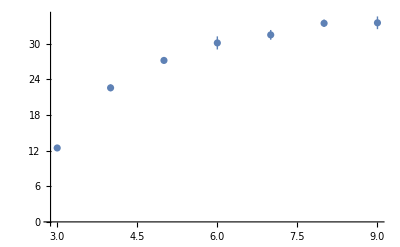

```mathematica
ListPlot[alphasd]
```

```mathematica
alphaval = {#[[1]], #[[2]]["Value"]}&/@alpha
```

{{3,15.0584},{4,18.7842},{5,21.2972},{6,23.553},{7,25.5193},{8,27.5254},{9,29.1334}}

```mathematica
alphastr = {#[[1]], ToString@SetPrecision[#[[2]]["Value"], 4]<>"("<>ToString@Ceiling[100#[[2]]["Uncertainty"]]<>")"}&/@alpha
```

{{3,15.06(6)},{4,18.78(5)},{5,21.30(6)},{6,23.55(17)},{7,25.52(2)},{8,27.53(18)},{9,29.13(17)}}

```mathematica
Export[plotsDir<>"/7-alpha.dat", alphastr];
```

```mathematica
fig[2] = ListLogLogPlot[alpha,
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"N", "\\alpha_N"},
FrameTicks->{{With[{ticks=15.+4Range[0,10]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->14cm
];
```

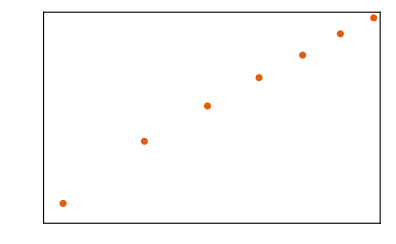

```mathematica
Magnify[fig[2], 1]
```

```mathematica
lm = LinearModelFit[Log[alphaval][[4;;]], {x}, x]
```

FittedModel[2.21158+0.528972 x]

```mathematica
fig[3]= LogLogPlot[Exp[lm[Log[$N]]], {$N, 2, 10},
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
PlotStyle->colors[[2]],
FrameLabel->MaTeX/@{"N", "\\alpha_N"},
FrameTicks->{{With[{ticks=15.+4Range[0,10]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->14cm
];
```

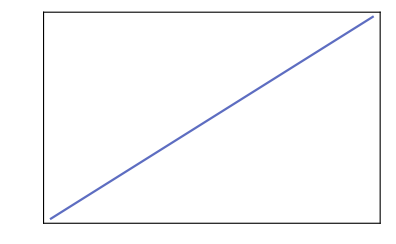

```mathematica
Magnify[fig[3], 1]
```

```mathematica
{a, b} = ToString/@SetPrecision[lm["BestFitParameters"] ,3];
leg = Column[{PointLegend[{colors[[1]]}, {MaTeX@"\\text{from }\\expval{\\Tr X^i X^i}"}], LineLegend[{colors[[2]]}, { MaTeX["\\text{fit:}\\quad "<>a<>" N^{"<>b<>"}"]}]}]
```

```mathematica
fig[4] = Legended[Show[fig[2], fig[3]], Placed[leg, {0.8, 0.3}]]
```

-Graphics-

```mathematica
Export[plotsDir<>"/7-alpha-fit.pdf", fig[4]];
```

```mathematica
alphaothers = Table[Module[{aa, bb, cc, dd, ee, σ1, σ2, randmat, alpha1, alpha2, alpha3, alpha4, alpha5}, (
{aa, bb, cc, dd} = Import["../../../runs/Stats-201/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"][[1;;10, 2;;]]ᵀ;
{ee} = Import["../../../runs/Stats-202/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"][[1;;10, 2;;]]ᵀ;
alpha1 = Around[2/($N #^2)&/@aa];
alpha2 = Around[(($N)^2-1)/($N #)&/@bb];
alpha3 = Around[(√(2(($N)^2-1)))/($N #)&/@cc];
randmat = Partition[(# - 1/($N)Tr[#]*IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1/(√($N)), $N], 10000*$K], $K];
σ1 = StandardDeviation[Tr[#[[1]].#[[2]]]&/@randmat];
σ2= StandardDeviation[Flatten[Map[Eigenvalues, randmat, {2}]]];
alpha4 = Around[σ1/#&/@dd];
alpha5 = Around[σ2^2/#^2&/@ee];
{$N, alpha1, alpha2, alpha3, alpha4, alpha5}
)], {$N, 3, 9}]
```

{{3,14.890.21,14.62.5,12.62.1,11.52.2,14.850.21},{4,18.90.4,18.51.1,16.11.2,16.11.6,18.90.4},{5,22.100.26,22.40.6,20.71.1,19.91.2,22.090.26},{6,24.530.22,24.70.5,22.50.9,22.71.2,24.520.22},{7,27.140.12,27.40.4,24.61.5,25.71.3,27.160.12},{8,29.280.16,29.120.33,25.61.3,27.91.3,29.280.16},{9,31.220.21,31.20.4,27.61.0,28.91.5,31.220.21}}

```mathematica
nicep[x_]:= Module[{a, b}, (
If[Quotient[x["Uncertainty"], 1]==0, (a = 4; b = 100), (a = 3; b=10)];ToString@SetPrecision[x["Value"], a]<>"("<>ToString@Ceiling[b*x["Uncertainty"]]<>")"
)]
```

```mathematica
alphastrother = Join[{#[[1]]}, nicep/@#[[2;;]]]&/@alphaothers
```

{{3,14.89(21),14.6(25),12.6(21),11.5(22),14.85(21)},{4,18.91(38),18.5(12),16.1(12),16.1(16),18.93(38)},{5,22.10(26),22.36(59),20.7(11),19.9(12),22.09(26)},{6,24.53(23),24.66(51),22.52(92),22.7(12),24.52(23)},{7,27.14(13),27.39(42),24.6(16),25.7(14),27.16(13)},{8,29.28(16),29.12(33),25.6(13),27.9(14),29.28(16)},{9,31.22(21),31.17(40),27.59(100),28.9(15),31.22(21)}}

```mathematica
alphafinal = Table[Join[alphastr[[k]], alphastrother[[k, 2;;]]], {k, 1, Length[alpha]}]
```

{{3,15.06(6),14.89(21),14.6(25),12.6(21),11.5(22),14.85(21)},{4,18.78(5),18.91(38),18.5(12),16.1(12),16.1(16),18.93(38)},{5,21.30(6),22.10(26),22.36(59),20.7(11),19.9(12),22.09(26)},{6,23.55(17),24.53(23),24.66(51),22.52(92),22.7(12),24.52(23)},{7,25.52(2),27.14(13),27.39(42),24.6(16),25.7(14),27.16(13)},{8,27.53(18),29.28(16),29.12(33),25.6(13),27.9(14),29.28(16)},{9,29.13(17),31.22(21),31.17(40),27.59(100),28.9(15),31.22(21)}}

```mathematica
Export[plotsDir<>"/7-alpha.dat", alphafinal];
```